# Dottie Number

### Author

Eric W. Weisstein
March 3, 2010

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Constants/DottieNumber.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/DottieNumber.html.

©2010 Wolfram Research, Inc. except for portions noted otherwise

### Code

```mathematica
DottieConstant=Root[{-Cos[#1]+#1&,0.7390851332151606416571598004269799139624141263097207627576`20.602059972540747}];

MakeBoxes[DottieConstant,TraditionalForm]:="r"
```

## Value

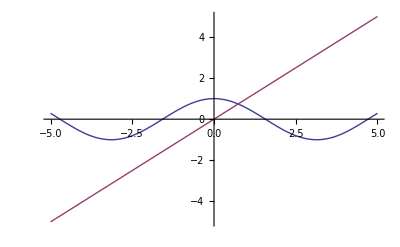

```mathematica
Plot[{Cos[x],x},{x,-5,5}]
```

#### V6

```mathematica
FindRoot[Cos[x]==x,{x,1}]
```

{x→0.739085}

#### V7

```mathematica
Reduce[Cos[x]==x,x,Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Cos[x]==x,x,Reals]

```mathematica
Reduce[Cos[x]==x&&x>0,x,Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Cos[x]==x&&x>0,x,Reals]

```mathematica
Reduce[Cos[x]==x&&0<x<10,x,Reals]
```

x==Root[{-Cos[#1]+#1&,0.73908513321516064166}]

#### V8

```mathematica
Solve[Cos[x] == x, x, Reals]
```

{{x→Root[{-Cos[#1]+#1&,0.73908513321516064165}]}}

```mathematica
Reduce[Cos[x]==x,x,Reals]
```

x==Root[{-Cos[#1]+#1&,0.73908513321516064165}]

```mathematica
FindInstance[Cos[x]==x,x, Reals]
```

{{x→Root[{Cos[#1]-#1&,0.739085133215160641655312087674}]}}

## Almost Integers

### (160/π)^(1/13) r==0.99999967661470791095

```mathematica
N[DottieConstant(160/π)^(1/13),20]
```

0.99999967661470791095

### ⅇ^(ⅇ^(π/3)-r)==5.0000000170647544117

K. Hammond

```mathematica
N[E^(E^(π/3)-Gamma[DottieConstant]),20]
```

5.0000000170647544117

## BBP-Type Formulas

```mathematica
<<Utilities`Simplify`
```

General::obspkg: "NumberTheory`Recognize`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

### Search

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,-3^k,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,16},{n,64},{p,1}],{-3^k,n,p}];//Timing
```

{61077.5,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,-3^k,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,16},{n,64},{p,2,2}],{-3^k,n,p}];//Timing
```

{99982.1,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,-3^k,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,16},{n,64},{p,3,3}],{-3^k,n,p}];//Timing
```

{98966.2,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,-2^k,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,16},{n,64},{p,1}],{-2^k,n,p}];//Timing
```

{85375.8,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,-2^k,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,16},{n,64},{p,2,2}],{-2^k,n,p}];//Timing
```

{103933.,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,-2^k,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,16},{n,64},{p,3,3}],{-2^k,n,p}];//Timing
```

{105524.,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,-1,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,0,0},{n,64},{p,1}],{-1,n,p}];//Timing
```

{4563.43,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,-1,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,0,0},{n,64},{p,2,2}],{-1,n,p}];//Timing
```

{4594.22,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,-1,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,0,0},{n,64},{p,3,3}],{-1,n,p}];//Timing
```

{4591.88,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,1,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,0,0},{n,64},{p,2,2}],{1,n,p}];//Timing
```

{3092.44,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,1,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,0,0},{n,64},{p,3,3}],{1,n,p}];//Timing
```

{3238.76,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,2^k,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,16},{n,64},{p,1}],{2^k,n,p}];//Timing
```

{84330.1,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,2^k,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,16},{n,64},{p,2,2}],{2^k,n,p}];//Timing
```

{106021.,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,2^k,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,16},{n,64},{p,3,3}],{2^k,n,p}];//Timing
```

{103497.,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,3^k,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,16},{n,64},{p,1}],{3^k,n,p}];//Timing
```

{35908.5,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,3^k,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,16},{n,64},{p,2,2}],{3^k,n,p}];//Timing
```

{45258.2,Null}

```mathematica
Monitor[Do[If[(b=FindBasis[DottieConstant,3^k,n,BasisPower->p,WorkingPrecision->300])=!={},Print[b]],{k,16},{n,64},{p,3,3}],{3^k,n,p}];//Timing
```

{28823.7,Null}